# Collatz Problem

### Author

Eric W. Weisstein
December 3, 2010

This notebook downloaded from http://mathworld.wolfram.com/notebooks/IntegerSequences/CollatzProblem.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/CollatzProblem.html.

For a list of Eric's math packages that may be needed to evaluate this notebook, see Mathematica Information Center's MathSource item 4775.  A list of Eric's utility packages that may be needed to evaluate this notebook may be downloaded from MathSource item 5087.

©2010 Wolfram Research, Inc. except for portions noted otherwise

### Code

```mathematica
Collatz[a0_Integer,maxits_:1000]:=NestWhileList[If[EvenQ[#],#/2,3#+1]&,a0,Unequal[#,1,-1,-10,-34]&,1,maxits]

Terras[a0_Integer,maxits_:1000]:=NestWhileList[If[EvenQ[#],#/2,(3#+1)/2]&,a0,Unequal[#,1,-1,-10,-34]&,1,maxits]
```

## Examples

```mathematica
Table[Collatz[n],{n,10}]//ColumnForm
```

{1}
{2,1}
{3,10,5,16,8,4,2,1}
{4,2,1}
{5,16,8,4,2,1}
{6,3,10,5,16,8,4,2,1}
{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}
{8,4,2,1}
{9,28,14,7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}
{10,5,16,8,4,2,1}

```mathematica
Collatz/@{4,-2,-5,-17}
```

{{4,2,1},{-2,-1},{-5,-14,-7,-20,-10},{-17,-50,-25,-74,-37,-110,-55,-164,-82,-41,-122,-61,-182,-91,-272,-136,-68,-34}}

```mathematica
Terras/@{4,-2,-5,-17}
```

{{4,2,1},{-2,-1},{-5,-7,-10},{-17,-25,-37,-55,-82,-41,-61,-91,-136,-68,-34}}

## Steps

A006577 (Formerly M4323)

```mathematica
Length[#]-1&/@Table[Collatz[n],{n,20}]
```

{0,1,7,2,5,8,16,3,19,6,14,9,9,17,17,4,12,20,20,7}

```mathematica
<<Graphics`Colors`
```

```mathematica
counts=Table[Length[Collatz[n]],{n,10^4}]-1;//Timing
```

{13.56 Second,Null}

```mathematica
Show[GraphicsArray[
Block[{$DisplayFunction=Identity},
ListPlot[Take[counts,#],PlotStyle->{Red,PointSize[.005]},
AxesLabel->TraditionalForm/@{n,StyleForm["steps to reach 1",FontSlant->Italic]}]&/@{10^3,10^4}
]]]
```

⁃GraphicsArray⁃

### Tripling/halving steps

```mathematica
steps=Divide@@@Partition[#,2,1]&/@Table[Collatz[n],{n,20}]
```

{{},{2},{3/10,2,5/16,2,2,2,2},{2,2},{5/16,2,2,2,2},{2,3/10,2,5/16,2,2,2,2},{7/22,2,11/34,2,17/52,2,2,13/40,2,2,2,5/16,2,2,2,2},{2,2,2},{9/28,2,2,7/22,2,11/34,2,17/52,2,2,13/40,2,2,2,5/16,2,2,2,2},{2,5/16,2,2,2,2},{11/34,2,17/52,2,2,13/40,2,2,2,5/16,2,2,2,2},{2,2,3/10,2,5/16,2,2,2,2},{13/40,2,2,2,5/16,2,2,2,2},{2,7/22,2,11/34,2,17/52,2,2,13/40,2,2,2,5/16,2,2,2,2},{15/46,2,23/70,2,35/106,2,53/160,2,2,2,2,2,5/16,2,2,2,2},{2,2,2,2},{17/52,2,2,13/40,2,2,2,5/16,2,2,2,2},{2,9/28,2,2,7/22,2,11/34,2,17/52,2,2,13/40,2,2,2,5/16,2,2,2,2},{19/58,2,29/88,2,2,2,11/34,2,17/52,2,2,13/40,2,2,2,5/16,2,2,2,2},{2,2,5/16,2,2,2,2}}

A006666 (Formerly M3733)

```mathematica
h=Count[#,_Integer]&/@steps
```

{0,1,5,2,4,6,11,3,13,5,10,7,7,12,12,4,9,14,14,6}

```mathematica
t=Count[#,_Rational]&/@steps
```

{0,0,2,0,1,2,5,0,6,1,4,2,2,5,5,0,3,6,6,1}

```mathematica
t+h
```

{0,1,7,2,5,8,16,3,19,6,14,9,9,17,17,4,12,20,20,7}

## Terras Modification

```mathematica
Collatz[7]
```

{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

```mathematica
Terras[7]
```

{7,11,17,26,13,20,10,5,8,4,2,1}

```mathematica
Table[Terras[n],{n,10}]//ColumnForm
```

{1}
{2,1}
{3,5,8,4,2,1}
{4,2,1}
{5,8,4,2,1}
{6,3,5,8,4,2,1}
{7,11,17,26,13,20,10,5,8,4,2,1}
{8,4,2,1}
{9,14,7,11,17,26,13,20,10,5,8,4,2,1}
{10,5,8,4,2,1}

### Terras Constant

```mathematica
H[x_]:=-x Log[2,x]-(1-x)Log[2,1-x]
θ=1/Log[2,3];
```

```mathematica
N[1-H[θ],20]
```

0.050044472811669365186

## Register Machine

Using 8 registers

Wolfram 2002, p. 100

## Tag System

De Mol  (2008)

```mathematica
CollatzTagIt[s_]:=If[StringLength[s]<2,"HALT",StringDrop[s,2]<>Switch[StringTake[s,1],"a","bc","b","a","c","aaa"]]
```

```mathematica
CollatzTagSystem[n_]:=NestWhileList[CollatzTag,StringJoin@@Table["a",{n}],StringLength[#]>1&]
```

```mathematica
NestList[CollatzTagIt,"aaa",25]
```

{aaa,abc,cbc,caaa,aaaaa,aaabc,abcbc,cbcbc,cbcaaa,caaaaaa,aaaaaaaa,aaaaaabc,aaaabcbc,aabcbcbc,bcbcbcbc,bcbcbca,bcbcaa,bcaaa,aaaa,aabc,bcbc,bca,aa,bc,a,HALT}

### 3

```mathematica
Terras[3]
```

{3,5,8,4,2,1}

```mathematica
c3=CollatzTagSystem[3]
```

{aaa,abc,cbc,caaa,aaaaa,aaabc,abcbc,cbcbc,cbcaaa,caaaaaa,aaaaaaaa,aaaaaabc,aaaabcbc,aabcbcbc,bcbcbcbc,bcbcbca,bcbcaa,bcaaa,aaaa,aabc,bcbc,bca,aa,bc,a}

```mathematica
StringLength/@Select[c3,StringMatchQ[#,"a"..]&]
```

{3,5,8,4,2,1}

### 7

```mathematica
Terras[7]
```

{7,11,17,26,13,20,10,5,8,4,2,1}

```mathematica
c7=CollatzTagSystem[7]
```

{aaaaaaa,aaaaabc,aaabcbc,abcbcbc,cbcbcbc,cbcbcaaa,cbcaaaaaa,caaaaaaaaa,aaaaaaaaaaa,aaaaaaaaabc,aaaaaaabcbc,aaaaabcbcbc,aaabcbcbcbc,abcbcbcbcbc,cbcbcbcbcbc,cbcbcbcbcaaa,cbcbcbcaaaaaa,cbcbcaaaaaaaaa,cbcaaaaaaaaaaaa,caaaaaaaaaaaaaaa,aaaaaaaaaaaaaaaaa,aaaaaaaaaaaaaaabc,aaaaaaaaaaaaabcbc,aaaaaaaaaaabcbcbc,aaaaaaaaabcbcbcbc,aaaaaaabcbcbcbcbc,aaaaabcbcbcbcbcbc,aaabcbcbcbcbcbcbc,abcbcbcbcbcbcbcbc,cbcbcbcbcbcbcbcbc,cbcbcbcbcbcbcbcaaa,cbcbcbcbcbcbcaaaaaa,cbcbcbcbcbcaaaaaaaaa,cbcbcbcbcaaaaaaaaaaaa,cbcbcbcaaaaaaaaaaaaaaa,cbcbcaaaaaaaaaaaaaaaaaa,cbcaaaaaaaaaaaaaaaaaaaaa,caaaaaaaaaaaaaaaaaaaaaaaa,aaaaaaaaaaaaaaaaaaaaaaaaaa,aaaaaaaaaaaaaaaaaaaaaaaabc,aaaaaaaaaaaaaaaaaaaaaabcbc,aaaaaaaaaaaaaaaaaaaabcbcbc,aaaaaaaaaaaaaaaaaabcbcbcbc,aaaaaaaaaaaaaaaabcbcbcbcbc,aaaaaaaaaaaaaabcbcbcbcbcbc,aaaaaaaaaaaabcbcbcbcbcbcbc,aaaaaaaaaabcbcbcbcbcbcbcbc,aaaaaaaabcbcbcbcbcbcbcbcbc,aaaaaabcbcbcbcbcbcbcbcbcbc,aaaabcbcbcbcbcbcbcbcbcbcbc,aabcbcbcbcbcbcbcbcbcbcbcbc,bcbcbcbcbcbcbcbcbcbcbcbcbc,bcbcbcbcbcbcbcbcbcbcbcbca,bcbcbcbcbcbcbcbcbcbcbcaa,bcbcbcbcbcbcbcbcbcbcaaa,bcbcbcbcbcbcbcbcbcaaaa,bcbcbcbcbcbcbcbcaaaaa,bcbcbcbcbcbcbcaaaaaa,bcbcbcbcbcbcaaaaaaa,bcbcbcbcbcaaaaaaaa,bcbcbcbcaaaaaaaaa,bcbcbcaaaaaaaaaa,bcbcaaaaaaaaaaa,bcaaaaaaaaaaaa,aaaaaaaaaaaaa,aaaaaaaaaaabc,aaaaaaaaabcbc,aaaaaaabcbcbc,aaaaabcbcbcbc,aaabcbcbcbcbc,abcbcbcbcbcbc,cbcbcbcbcbcbc,cbcbcbcbcbcaaa,cbcbcbcbcaaaaaa,cbcbcbcaaaaaaaaa,cbcbcaaaaaaaaaaaa,cbcaaaaaaaaaaaaaaa,caaaaaaaaaaaaaaaaaa,aaaaaaaaaaaaaaaaaaaa,aaaaaaaaaaaaaaaaaabc,aaaaaaaaaaaaaaaabcbc,aaaaaaaaaaaaaabcbcbc,aaaaaaaaaaaabcbcbcbc,aaaaaaaaaabcbcbcbcbc,aaaaaaaabcbcbcbcbcbc,aaaaaabcbcbcbcbcbcbc,aaaabcbcbcbcbcbcbcbc,aabcbcbcbcbcbcbcbcbc,bcbcbcbcbcbcbcbcbcbc,bcbcbcbcbcbcbcbcbca,bcbcbcbcbcbcbcbcaa,bcbcbcbcbcbcbcaaa,bcbcbcbcbcbcaaaa,bcbcbcbcbcaaaaa,bcbcbcbcaaaaaa,bcbcbcaaaaaaa,bcbcaaaaaaaa,bcaaaaaaaaa,aaaaaaaaaa,aaaaaaaabc,aaaaaabcbc,aaaabcbcbc,aabcbcbcbc,bcbcbcbcbc,bcbcbcbca,bcbcbcaa,bcbcaaa,bcaaaa,aaaaa,aaabc,abcbc,cbcbc,cbcaaa,caaaaaa,aaaaaaaa,aaaaaabc,aaaabcbc,aabcbcbc,bcbcbcbc,bcbcbca,bcbcaa,bcaaa,aaaa,aabc,bcbc,bca,aa,bc,a}

```mathematica
StringLength/@Select[c7,StringMatchQ[#,"a"..]&]
```

{7,11,17,26,13,20,10,5,8,4,2,1}

## Enrique Zeleny base-6 2-D CA

Note that this CA considers wraparound rules that effectively make it nonlocal

http://demonstrations.wolfram.com/CollatzProblemAsACellularAutomaton/

```mathematica
Zeleny[n_]:=Transpose[DeleteCases[Transpose[
 (NestWhileList[Partition[#1,3,1,2]/.
{a_,b_,c_}->If[b==6,If[EvenQ[a],6,4],3 Mod[a,2]+Quotient[b,2]/. 0:>6/;a==6]&,Flatten[{IntegerDigits[n,6],Table[6,{50}]}],
!MatchQ[#1,{(6)..,1,(6)..}]&]/. Thread[Range[6]->Range[6,1,-1]])],{1..}]]
```

```mathematica
rules={0->Red,1->Yellow,2->Green,3->Hue[.5],4->Blue,5->Purple,6->White};
```

### 3

```mathematica
Zeleny[3]
```

{{4,1,1},{6,3,1},{1,2,1},{1,5,3},{1,6,5},{1,1,3},{1,1,5},{1,1,6}}

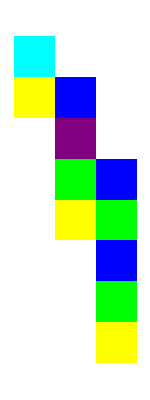

```mathematica
ArrayPlot[Mod[-Zeleny[3],7],ColorRules->rules]
```

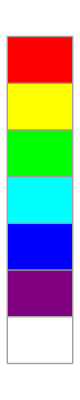

```mathematica
ArrayPlot[Transpose@{Range[0,6]},ColorRules->rules,Mesh->True]
```

```mathematica
Mod[-DeleteCases[Zeleny[3],1,{2}],7]
```

{{3},{1,4},{5},{2,4},{1,2},{4},{2},{1}}

```mathematica
FromDigits[#,6]&/@%
```

{3,10,5,16,8,4,2,1}

```mathematica
Collatz[3]
```

{3,10,5,16,8,4,2,1}

### 7

```mathematica
Zeleny[7]
```

{{6,6,1,1,1,1,1},{1,4,3,1,1,1,1},{1,6,2,1,1,1,1},{1,1,2,3,1,1,1},{1,1,5,2,1,1,1},{1,1,6,5,3,1,1},{1,1,1,3,5,1,1},{1,1,1,5,6,1,1},{1,1,1,6,0,3,1},{1,1,1,1,4,5,1},{1,1,1,1,6,3,1},{1,1,1,1,1,2,1},{1,1,1,1,1,5,3},{1,1,1,1,1,6,5},{1,1,1,1,1,1,3},{1,1,1,1,1,1,5},{1,1,1,1,1,1,6}}

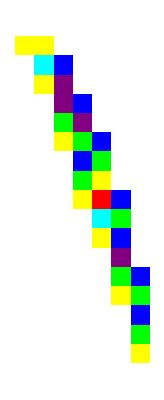

```mathematica
ArrayPlot[Mod[-Zeleny[7],7],rules]
```

```mathematica
Mod[-DeleteCases[Zeleny[7],1,{2}],7]
```

{{1,1},{3,4},{1,5},{5,4},{2,5},{1,2,4},{4,2},{2,1},{1,0,4},{3,2},{1,4},{5},{2,4},{1,2},{4},{2},{1}}

```mathematica
FromDigits[#,6]&/@%
```

{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

```mathematica
Collatz[7]
```

{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

## Bruschi Quasi-CA

### Base-2

```mathematica
RuleIA[d_]:={0,-1}+StringPosition[d,"01"~~Shortest[___]~~"00",1][[1]]
```

```mathematica
RuleIBC[d_]:=Module[{i=RuleIA[d],p},
p=StringPosition[StringDrop[d,i[[2]]],"11"~~Shortest[___]~~"00",Overlaps->False];
If[p==={},{i},Join[{i},i[[-1]]+{1,-1}+#&/@p]]
]
```

```mathematica
CAStep[d_]:=Module[{t=Flatten[Range@@@RuleIBC[d]],u=ToExpression[Characters[d]]},
(StringJoin@@(ToString/@Mod[Table[u[[n+1]]+u[[n+2]]+Boole[MemberQ[t,n+1]],{n,Length[u]-2}],2]
)<>"00")
]
```

```mathematica
AnnotateStep[d_]:=Row[MapAt[OverDot,Characters[d],List/@Flatten[Range@@@RuleIBC[d]]]]
```

```mathematica
DecodeCAStrings[l_]:=FromDigits[#,2]&/@((Reverse/@ToExpression[Characters[l]])/.List[x___,0..]:>{x})
```

```mathematica
EncodeCAString[d_,n_:10]:=StringJoin@@Table["0",{n}]<>StringJoin@@(ToString/@Reverse@IntegerDigits[d,2])<>"00"
```

#### Initial Example

```mathematica
AnnotateStep/@(l=Most[FixedPointList[CAStep,"00000011010000111010001011001000"]])//Column
```

00000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]0001OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]00101OverDot[1]OverDot[0]01000
0000OverDot[0]OverDot[1]OverDot[0]00100101000101OverDot[1]OverDot[1]OverDot[0]01OverDot[1]OverDot[1]OverDot[0]000
0000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]01OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]000
00000OverDot[0]OverDot[1]OverDot[0]01OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]00010000010000
00000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]010001001OverDot[1]OverDot[0]0001OverDot[1]OverDot[0]0000
0000OverDot[0]OverDot[1]OverDot[0]001OverDot[1]OverDot[1]OverDot[0]01OverDot[1]OverDot[0]OverDot[1]OverDot[0]0100100100000
0000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]0001OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]00000
000000000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]010100100101000000
00000000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]000000
0000000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]01001OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]000000
000000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]0010000000
00000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]01OverDot[1]OverDot[0]0000101OverDot[1]OverDot[0]0000000
0000000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]010001OverDot[1]OverDot[1]OverDot[0]0100000000
00000000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]010101OverDot[1]OverDot[1]OverDot[0]00000000
000000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]00000000
00000000OverDot[0]OverDot[1]OverDot[0]01OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]00001000000000
00000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]001OverDot[1]OverDot[0]000000000
0000000OverDot[0]OverDot[1]OverDot[0]01OverDot[1]OverDot[0]001010010000000000
0000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]0101OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]0000000000
000000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]010100000000000
0000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]0101OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]00000000000
000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]00000000000
00000OverDot[0]OverDot[1]OverDot[0]01OverDot[1]OverDot[1]OverDot[0]01OverDot[1]OverDot[0]001000000000000
00000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]0101OverDot[1]OverDot[0]000000000000
0000OverDot[0]OverDot[1]OverDot[0]000101OverDot[1]OverDot[1]OverDot[1]OverDot[0]010000000000000
0000OverDot[0]OverDot[1]OverDot[0]01OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]0000000000000
0000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]01001OverDot[1]OverDot[0]OverDot[1]OverDot[0]0000000000000
000OverDot[0]OverDot[1]OverDot[0]001OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]000100000000000000
000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]001001OverDot[1]OverDot[0]00000000000000
0000000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]01000000000000000
00000000OverDot[0]OverDot[1]OverDot[0]001OverDot[1]OverDot[1]OverDot[0]000000000000000
00000000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]000000000000000
00000000000000OverDot[0]OverDot[1]OverDot[0]000000000000000

```mathematica
CAStep["00011010000111010001011001000"]
```

00010001001010001011100111000

```mathematica
CAStep[%]
```

00000010011101101000010000010

```mathematica
DecodeCAStrings[l]
```

{5052171,7578257,5683693,2131385,1598539,2397809,1798357,42149,7903,11855,17783,26675,40013,15005,5627,8441,6331,9497,7123,10685,4007,6011,9017,6763,10145,7609,5707,8561,6421,301,113,85,1}

```mathematica
Collatz[First[%]]
```

{5052171,15156514,7578257,22734772,11367386,5683693,17051080,8525540,4262770,2131385,6394156,3197078,1598539,4795618,2397809,7193428,3596714,1798357,5395072,2697536,1348768,674384,337192,168596,84298,42149,126448,63224,31612,15806,7903,23710,11855,35566,17783,53350,26675,80026,40013,120040,60020,30010,15005,45016,22508,11254,5627,16882,8441,25324,12662,6331,18994,9497,28492,14246,7123,21370,10685,32056,16028,8014,4007,12022,6011,18034,9017,27052,13526,6763,20290,10145,30436,15218,7609,22828,11414,5707,17122,8561,25684,12842,6421,19264,9632,4816,2408,1204,602,301,904,452,226,113,340,170,85,256,128,64,32,16,8,4,2,1}

```mathematica
Cases[%,_?OddQ]
```

{5052171,7578257,5683693,2131385,1598539,2397809,1798357,42149,7903,11855,17783,26675,40013,15005,5627,8441,6331,9497,7123,10685,4007,6011,9017,6763,10145,7609,5707,8561,6421,301,113,85,1}

#### 25

```mathematica
EncodeCAString[25]
```

001001100

```mathematica
(l=Most[FixedPointList[CAStep,EncodeCAString[25]]])//Column
```

001001100
001100100
010111000
001101000
010001000
010110000
001010000
000010000

```mathematica
DecodeCAStrings[l]
```

{25,19,29,11,17,13,5,1}

```mathematica
Collatz[25]
```

{25,76,38,19,58,29,88,44,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

```mathematica
Cases[%,_?OddQ]
```

{25,19,29,11,17,13,5,1}

#### 163

```mathematica
EncodeCAString[163]
```

001100010100

```mathematica
(l=Most[FixedPointList[CAStep,EncodeCAString[163]]])//Column
```

001100010100
010101111000
000011101000
000110001000
001010110000
000001010000
000000010000

```mathematica
DecodeCAStrings[l]
```

{163,245,23,35,53,5,1}

```mathematica
Collatz[163]
```

{163,490,245,736,368,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

```mathematica
Cases[%,_?OddQ]
```

{163,245,23,35,53,5,1}

#### Check Odd

```mathematica
Collatz[2]
```

{2,1}

```mathematica
Grid[Table[{DecodeCAStrings[Most[FixedPointList[CAStep,EncodeCAString[n]]]],Cases[Collatz[n],_?OddQ]},{n,15}],Dividers->All,Alignment->Left]//TraditionalForm
```

{1} | {1}
{1} | {1}
{3,5,1} | {3,5,1}
{1} | {1}
{5,1} | {5,1}
{3,5,1} | {3,5,1}
{7,11,17,13,5,1} | {7,11,17,13,5,1}
{1} | {1}
{9,7,11,17,13,5,1} | {9,7,11,17,13,5,1}
{5,1} | {5,1}
{11,17,13,5,1} | {11,17,13,5,1}
{3,5,1} | {3,5,1}
{13,5,1} | {13,5,1}
{7,11,17,13,5,1} | {7,11,17,13,5,1}
{15,23,35,53,5,1} | {15,23,35,53,5,1}

```mathematica
tf=Equal@@@Table[{DecodeCAStrings[Most[FixedPointList[CAStep,EncodeCAString[n,20]]]],Cases[Collatz[n],_?OddQ]},{n,200}];
```

```mathematica
Position[tf,False]//Flatten
```

{}

```mathematica
AnnotateStep/@Most[FixedPointList[CAStep,EncodeCAString[27,21]]]
```

{00000000000000000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]0,0000000000000000000OverDot[0]OverDot[1]OverDot[0]010100,0000000000000000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]00,000000000000000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]00,00000000000000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]001000,0000000000000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]000,000000000000000OverDot[0]OverDot[1]OverDot[0]0001010000,000000000000000OverDot[0]OverDot[1]OverDot[0]01OverDot[1]OverDot[1]OverDot[1]OverDot[0]0000,000000000000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]0000,00000000000000OverDot[0]OverDot[1]OverDot[0]01000100000,00000000000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]01OverDot[1]OverDot[0]00000,0000000000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]01000000,000000000000OverDot[0]OverDot[1]OverDot[0]0101OverDot[1]OverDot[1]OverDot[0]000000,000000000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]000000,00000000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]000010000000,0000000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]001OverDot[1]OverDot[0]0000000,000000000OverDot[0]OverDot[1]OverDot[0]0010100100000000,000000000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]00000000,0000000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]0101000000000,000000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]000000000,00000000OverDot[0]OverDot[1]OverDot[0]01OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]000000000,00000000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]0010000000000,0000000OverDot[0]OverDot[1]OverDot[0]010101OverDot[1]OverDot[0]0000000000,0000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]0100000000000,000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]00000000000,00000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]01OverDot[1]OverDot[0]OverDot[1]OverDot[0]00000000000,0000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]0001000000000000,000OverDot[0]OverDot[1]OverDot[1]OverDot[0]0101001OverDot[1]OverDot[0]000000000000,00OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]010000000000000,000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]001OverDot[1]OverDot[1]OverDot[0]0000000000000,00OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]0000000000000,0OverDot[0]OverDot[1]OverDot[1]OverDot[0]00000000100000000000000,OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]0000001OverDot[1]OverDot[0]00000000000000,00OverDot[0]OverDot[1]OverDot[0]00001001000000000000000,00OverDot[0]OverDot[1]OverDot[0]001OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]000000000000000,00OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]001010000000000000000,0000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[1]OverDot[0]0000000000000000,00000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]0000000000000000,0000OverDot[0]OverDot[1]OverDot[1]OverDot[0]00100000000000000000,000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]00000000000000000,000000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]00000000000000000,00000000OverDot[0]OverDot[1]OverDot[0]00000000000000000}

```mathematica
AnnotateStep/@Most[FixedPointList[CAStep,EncodeCAString[7]]]
```

{000000OverDot[0]OverDot[1]OverDot[1]OverDot[1]OverDot[0]0,00000OverDot[0]OverDot[1]OverDot[1]OverDot[0]OverDot[1]OverDot[0]0,0000OverDot[0]OverDot[1]OverDot[0]00100,0000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[1]OverDot[0]00,00000OverDot[0]OverDot[1]OverDot[0]OverDot[1]OverDot[0]00,0000000OverDot[0]OverDot[1]OverDot[0]00}

#### x+2^300

```mathematica
Length[l=Most[FixedPointList[CAStep,EncodeCAString[2^300+7,30]]]]//Timing
```

{1.10882,722}

```mathematica
Length[l2=Collatz[2^300+7,10^4]]//Timing
```

{0.008898,2165}

```mathematica
DecodeCAStrings[l]==Cases[l2,_?OddQ]
```

True

```mathematica
ArrayPlot[Transpose[ToExpression[Characters[l]]],PixelConstrained->1]
```

-Graphics-

### Base-3

To do...

## OEIS

```mathematica
<<Utilities`EISFormat`
```

EISFormat.m version 1.06 by Olivier Gerard and Eric W. Weisstein

e-mail FormatSequence to njas@research.att.com

e-mail LookupFormat   to sequences@research.att.com

or superseeker@research.att.com (single line only)

```mathematica
FormatSequence[Flatten[Table[Collatz[n],{n,20}]],70165,1,
Name->"Triangle of Collatz problem sequences for starting values a0=1, a0=2, ...",
html["Collatz Problem"],
Keyw->{"easy","tri"},
Cross->{6667}
]
```

FormatSequence::HeyYou: My respects to you, Master "Eric".

%I A070165 
%S A070165 1,2,1,3,10,5,16,8,4,2,1,4,2,1,5,16,8,4,2,1,6,3,10,5,16,8,4,2,1,7,22,
%T A070165 11,34,17,52,26,13,40,20,10,5,16,8,4,2,1,8,4,2,1,9,28,14,7,22,11,34,
%U A070165 17,52,26,13,40,20,10,5,16,8,4,2,1,10,5,16,8,4,2,1,11,34,17,52,26,13
%N A070165 Triangle of Collatz problem sequences for starting values a0=1, a0=2, ...
%H A070165 E. W. Weisstein, <a href="http://mathworld.wolfram.com/CollatzProblem.html">Collatz Problem</a>
%Y A070165 Cf. A006667.
%A A070165 Eric W. Weisstein (eric@weisstein.com), Apr 23, 2002
%O A070165 1,2
%K A070165 nonn,easy,tri

```mathematica
FormatSequence[Table[Position[Table[Collatz[n],{n,100}],n,{2},1][[1,1]],
{n,100}],70167,1,
Name->"a(n) is the smallest starting value a0 which produces a Collatz sequence in which n occurs.",
html["Collatz Sequence"],
Cross->{6667,70165}
]
```

FormatSequence::HeyYou: My respects to you, Master "Eric".

%I A070167 
%S A070167 1,2,3,3,3,6,7,3,9,3,7,12,7,9,15,3,7,18,19,7,21,7,15,24,25,7,27,9,19,
%T A070167 30,27,21,33,7,15,36,37,25,39,7,27,42,43,19,45,15,27,48,43,33,51,7,15,
%U A070167 54,55,37,57,19,39,60,27,27,63,21,43,66,39,45,69,15,27,72,73,43,75,25
%N A070167 a(n) is the smallest starting value a0 which produces a Collatz sequence in which n occurs.
%H A070167 E. W. Weisstein, <a href="http://mathworld.wolfram.com/CollatzSequence.html">Collatz Sequence</a>
%Y A070167 Cf. A006667,A070165.
%A A070167 Eric W. Weisstein (eric@weisstein.com), Apr 23, 2002
%O A070167 1,2
%K A070167 nonn

```mathematica
FormatSequence[Flatten[Table[Terras[n],{n,20}]],70168,1,
Name->"Triangle of Terras-modified Collatz problem sequences for starting values a0=1, a0=2, ...",
html["Collatz Problem"],
Keyw->{"easy","tri"}
]
```

FormatSequence::HeyYou: My respects to you, Master "Eric".

%I A070168 
%S A070168 1,2,1,3,5,8,4,2,1,4,2,1,5,8,4,2,1,6,3,5,8,4,2,1,7,11,17,26,13,20,10,
%T A070168 5,8,4,2,1,8,4,2,1,9,14,7,11,17,26,13,20,10,5,8,4,2,1,10,5,8,4,2,1,11,
%U A070168 17,26,13,20,10,5,8,4,2,1,12,6,3,5,8,4,2,1,13,20,10,5,8,4,2,1,14,7,11
%N A070168 Triangle of Terras-modified Collatz problem sequences for starting values a0=1, a0=2, ...
%H A070168 E. W. Weisstein, <a href="http://mathworld.wolfram.com/CollatzProblem.html">Collatz Problem</a>
%A A070168 Eric W. Weisstein (eric@weisstein.com), Apr 23, 2002
%O A070168 1,2
%K A070168 nonn,easy,tri